```mathematica
<<Teukolsky`
```

## Compute retarded field data

```mathematica
a=0;
p=6.0;
e=0;
x=1;
```

```mathematica
orbit=KerrGeoOrbit[a,p,e,x];
```

```mathematica
Monitor[ϕl=Table[Sum[TeukolskyPointParticleMode[0,l,m,orbit]["ExtendedHomogeneous"->"ℐ"][p]SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}],{l,0,20}];,{l,m}]
```

## Regularization parameters

Taken from Phys. Rev. D 82, 104023 (2012) and Phys. Rev. D 89, 024030 (2014). Soon this can be replaced with the Regularization package, but for now we just copy in the explicit expressions.

```mathematica
With[{L=orbit["AngularMomentum"],E0=orbit["Energy"],r0=p,M=1},
Φl[0]=(2 EllipticK[L^2/(L^2+r0^2)])/(π √(L^2+r0^2));
Φl[2]=((4 L^4 M+L^2 (10 M-r0) r0^2+r0^4 (6 M+(-1+2 E0^2) r0)) EllipticE[L^2/(L^2+r0^2)]-r0^2 (2 L^2 M+r0^2 (2 M+E0^2 r0)) EllipticK[L^2/(L^2+r0^2)])/((-1+2 l) (3+2 l) π r0^3 (L^2+r0^2)^(3/2));
Φl[4]=(3 (2 (256 L^14 M^2-960 L^12 M (5 M-3 r0) r0^2-8 L^10 M r0^4 (3383 M+16 (-110+17 E0^2) r0)-4 L^8 M r0^6 (13874 M+3 (-2305+722 E0^2) r0)+L^6 r0^8 (-56304 M^2+2 (13705-6526 E0^2) M r0+15 r0^2)+L^4 r0^10 (-29140 M^2+2 (6905-4511 E0^2) M r0+15 (4+E0^2) r0^2)+r0^14 (-300 M^2+2 (25+17 E0^2) M r0+15 (2-7 E0^2+4 E0^4) r0^2)-3 L^2 r0^12 (2208 M^2+2 (-485+404 E0^2) M r0+5 (-5+6 E0^2+4 E0^4) r0^2)) EllipticE[L^2/(L^2+r0^2)]+r0^2 (-256 L^12 M^2+32 L^10 M (157 M-90 r0) r0^2+4 L^6 M r0^6 (8981 M+130 (-34+13 E0^2) r0)+8 L^8 M r0^4 (2832 M+17 (-85+16 E0^2) r0)+L^4 r0^8 (25856 M^2+12 (-1035+607 E0^2) M r0-15 r0^2)+L^2 r0^10 (7908 M^2+8 (-455+344 E0^2) M r0+15 (-2+8 E0^2+3 E0^4) r0^2)+r0^12 (600 M^2+4 (-55+13 E0^2) M r0-15 (1-8 E0^2+5 E0^4) r0^2)) EllipticK[L^2/(L^2+r0^2)]))/(20 (-3+2 l) (-1+2 l) (3+2 l) (5+2 l) π r0^10 (L^2+r0^2)^(7/2));
]
```

## Regularize

Verify regularization is working:

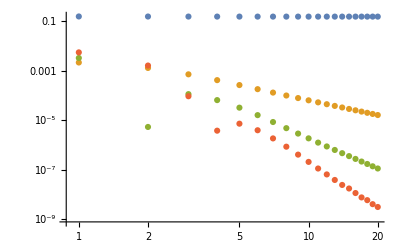

```mathematica
ListLogLogPlot[Abs[{ϕl,ϕl-Φl[0],ϕl-Table[Φl[0]+Φl[2],{l,0,20}],ϕl-Table[Φl[0]+Φl[2]+Φl[4],{l,0,20}]}],DataRange->{0,20}]
```

Compare against the value quoted in Table I of [PRD 89, 044046 (2014)]

```mathematica
Φreg=-5.454828078597 10^-3;
```

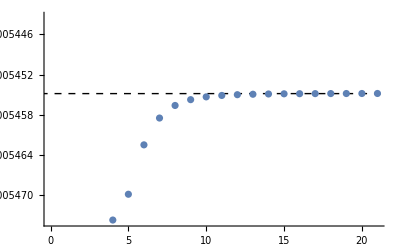

```mathematica
Show[ListPlot[Accumulate[Re[ϕl-Table[Φl[0]+Φl[2]+Φl[4],{l,0,20}]]]],Graphics[{Black,Dashed,InfiniteLine[{20,Φreg},{1,0}]}]]
```

```mathematica
Total[Re[ϕl-Table[Φl[0]+Φl[2]+Φl[4],{l,0,20}]]]
```

-0.00545481